# GW Spectrum

```mathematica
ClearAll["Global`*"]
```

```mathematica
DumpGet[NotebookDirectory[]<>"Spline.m"]
DumpGet[NotebookDirectory[]<>"Veff.m"]
λmax=<<(NotebookDirectory[]<>"lambda_max.m");
λmin=<<(NotebookDirectory[]<>"lambda_min.m");
```

```mathematica
SetDirectory[NotebookDirectory[]]
<<anybubble.m
<<powell.m
Options[FindBubble]
```

/Users/isaac/Dropbox/Project/2021-9-local_EWBG_parity/02-Work/phase_transition

{Verbose→False,SpaceTimeDimension→3,StartAnalyticFraction→1/100,EndAnalyticFraction→1/100,MaxIntervalGrowth→30,MaxReadjustments→20,InitialProfilePoints→{},PowellVerbosity→1,MaxIterations→500,AccuracyGoal→Automatic,WorkingPrecision→MachinePrecision}

## α and β parameter

### λmin

```mathematica
Plot[VBParwani[λmin,ϕ,66000.],{ϕ,0,130000}]
```

-Graphics-

```mathematica
T1=66030.;
fitting=Table[{ϕ,VBParwani[λmin,ϕ,T1]},{ϕ,1,130000,200}];
Vfit[ϕ_]=Fit[fitting,{1,ϕ,ϕ^2,ϕ^3,ϕ^4,ϕ^5,ϕ^6,ϕ^7,ϕ^8,ϕ^9,ϕ^10,ϕ^11,ϕ^12,ϕ^13,ϕ^14,ϕ^15,ϕ^16,ϕ^17,ϕ^18,ϕ^19,ϕ^20},ϕ];
xr=x/.Minimize[{Vfit[x]-Vfit[0],{80000<x<150000}},x][[2]];
SbyT=(FindBubble[Vfit[x[1]]-Vfit[0],x,{xr},{0}]/T1)[[1]]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

....................

140.086

```mathematica
Tnλmin=66030;
gstar=143;
bouncelistλmin=Table[Clear[fitting,Vfit];
fitting=Table[{ϕ,VBParwani[λmin,ϕ,T1]},{ϕ,1,130000,200}];
Vfit[ϕ_]=Fit[fitting,{1,ϕ,ϕ^2,ϕ^3,ϕ^4,ϕ^5,ϕ^6,ϕ^7,ϕ^8,ϕ^9,ϕ^10,ϕ^11,ϕ^12,ϕ^13,ϕ^14,ϕ^15,ϕ^16,ϕ^17,ϕ^18,ϕ^19,ϕ^20},ϕ];xr=x/.Minimize[{Vfit[x]-Vfit[0],{80000<x<150000}},x][[2]];ΔV=Minimize[{Vfit[v]-Vfit[0],{80000<v<150000}},v][[1]];xr/T1;SbyT=(FindBubble[Vfit[x[1]]-Vfit[0],x,{xr},{0}]/T1)[[1]];{T1,SbyT,ΔV},{T1,Tn-15.,Tn+15.,3.}];
bounceplotλmin=bouncelistλmin[[All,{1,2}]]
latentheatdiffλmin=bouncelistλmin[[All,{1,3}]]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

................................................................................................................................................................................................................................................

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

General::stop: Further output of FindMaximum::cvmit will be suppressed during this calculation.

{{66015.,130.191},{66018.,132.077},{66021.,134.044},{66024.,136.023},{66027.,138.041},{66030.,140.086},{66033.,142.161},{66036.,144.274},{66039.,146.417},{66042.,148.594},{66045.,150.715}}

{{66015.,-9.57772×10^16},{66018.,-9.50421×10^16},{66021.,-9.43081×10^16},{66024.,-9.35754×10^16},{66027.,-9.28438×10^16},{66030.,-9.21134×10^16},{66033.,-9.13841×10^16},{66036.,-9.0656×10^16},{66039.,-8.99292×10^16},{66042.,-8.92035×10^16},{66045.,-8.84789×10^16}}

0.0180573

45315.9

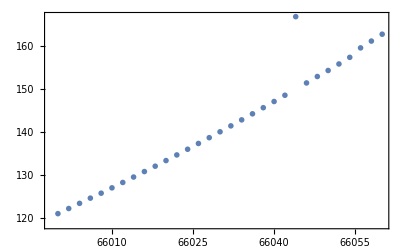

```mathematica
s3Tλmin=Interpolation[bounceplotλmin];
deltaVλmin=Interpolation[latentheatdiffλmin];
ρradλmin=(Pi^2/30*gstar*Tnλmin^4);
αλmin=(-ΔV+Tn*deltaVλmin'[Tnλmin])/ρradλmin
(*α paramter*)
βHλmin=Tnλmin*s3Tλmin'[Tnλmin]
(*beta paramter*)
ListPlot[bounceplotλmin]
```

### λmax

```mathematica
Plot[VBParwani[λmax,ϕ,82000.],{ϕ,0,120000}]
```

-Graphics-

```mathematica
T1=82122.;
fitting=Table[{ϕ,VBParwani[λmax,ϕ,T1]},{ϕ,1,120000,200}];
Vfit[ϕ_]=Fit[fitting,{1,ϕ,ϕ^2,ϕ^3,ϕ^4,ϕ^5,ϕ^6,ϕ^7,ϕ^8,ϕ^9,ϕ^10,ϕ^11,ϕ^12,ϕ^13,ϕ^14,ϕ^15,ϕ^16,ϕ^17,ϕ^18,ϕ^19,ϕ^20},ϕ];
xr=x/.Minimize[{Vfit[x]-Vfit[0],{60000<x<120000}},x][[2]];
SbyT=(FindBubble[Vfit[x[1]]-Vfit[0],x,{xr},{0}]/T1)[[1]]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

............................

140.322

```mathematica
Tnλmax=82122.;
gstar=100;
bouncelistλmax=Table[Clear[fitting,Vfit];
fitting=Table[{ϕ,VBParwani[λmax,ϕ,T1]},{ϕ,1,120000,200}];
Vfit[ϕ_]=Fit[fitting,{1,ϕ,ϕ^2,ϕ^3,ϕ^4,ϕ^5,ϕ^6,ϕ^7,ϕ^8,ϕ^9,ϕ^10,ϕ^11,ϕ^12,ϕ^13,ϕ^14,ϕ^15,ϕ^16,ϕ^17,ϕ^18,ϕ^19,ϕ^20},ϕ];xr=x/.Minimize[{Vfit[x]-Vfit[0],{80000<x<150000}},x][[2]];ΔV=Minimize[{Vfit[v]-Vfit[0],{80000<v<150000}},v][[1]];xr/T1;SbyT=(FindBubble[Vfit[x[1]]-Vfit[0],x,{xr},{0}]/T1)[[1]];{T1,SbyT,ΔV},{T1,Tnλmax-15.,Tnλmax+15.,1.}];
bounceplotλmax=bouncelistλmax[[All,{1,2}]]
latentheatdiffλmax=bouncelistλmax[[All,{1,3}]]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

.............................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

General::stop: Further output of FindMaximum::cvmit will be suppressed during this calculation.

PowellHybrid::tooSmall: PowellHybrid reduced stepsize to too-small value 4.61083×10^-8

{{82107.,128.394},{82108.,129.137},{82109.,129.889},{82110.,130.647},{82111.,131.408},{82112.,132.167},{82113.,132.96},{82114.,133.746},{82115.,134.528},{82116.,135.328},{82117.,136.125},{82118.,136.94},{82119.,137.771},{82120.,138.581},{82121.,139.448},{82122.,140.341},{82123.,141.191},{82124.,142.069},{82125.,142.994},{82126.,143.976},{82127.,144.838},{82128.,145.836},{82129.,146.872},{82130.,147.654},{82131.,148.693},{82132.,149.623},{82133.,150.645},{82134.,151.628},{82135.,152.694},{82136.,153.724},{82137.,154.745}}

{{82107.,-5.71535×10^16},{82108.,-5.69359×10^16},{82109.,-5.67184×10^16},{82110.,-5.65012×10^16},{82111.,-5.6284×10^16},{82112.,-5.60671×10^16},{82113.,-5.58503×10^16},{82114.,-5.56337×10^16},{82115.,-5.54172×10^16},{82116.,-5.52009×10^16},{82117.,-5.49848×10^16},{82118.,-5.47688×10^16},{82119.,-5.4553×10^16},{82120.,-5.43373×10^16},{82121.,-5.41218×10^16},{82122.,-5.39065×10^16},{82123.,-5.36914×10^16},{82124.,-5.34764×10^16},{82125.,-5.32615×10^16},{82126.,-5.30469×10^16},{82127.,-5.28324×10^16},{82128.,-5.2618×10^16},{82129.,-5.24038×10^16},{82130.,-5.21898×10^16},{82131.,-5.1976×10^16},{82132.,-5.17623×10^16},{82133.,-5.15488×10^16},{82134.,-5.13355×10^16},{82135.,-5.11223×10^16},{82136.,-5.09093×10^16},{82137.,-5.06964×10^16}}

0.00666595

72516.2

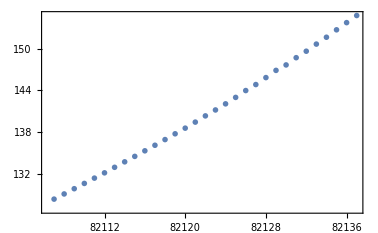

```mathematica
s3Tλmax=Interpolation[bounceplotλmax];
deltaVλmax=Interpolation[latentheatdiffλmax];
ρradλmax=(Pi^2/30*gstar*Tnλmax^4);
αλmax=(-ΔV+Tn*deltaVλmax'[Tnλmax])/ρradλmax
(*α paramter*)
βHλmax=Tnλmax*s3Tλmax'[Tnλmax]
(*beta paramter*)
ListPlot[bounceplotλmax]
```

## GW in low wall speed

### Sound wave

```mathematica
fsou[vb_,βH_,Tn_]:=1.9*10^(-5)*(143/100)^(1/6)*(Tn/100)*(βH)/vb;
gstar=143;
(*A peak frequency*)
κA[vb_,α_]:=vb^(6/5)(6.9α)/(1.36-0.037 √α+α);
κB[α_]:=α^(2/5)/(0.017+(0.997+α)^(2/5));
κ[vb_,α_]:=κA[vb,α] ((1/√3)^(11/5)κB[α])/(((1/√3)^(11/5)-vb^(11/5))κB[α]+vb (1/√3)^(6/5)κA[vb,α]);
(*An efficiency factor*)
Htaushock[vb_,α_,βH_]:=Min[1,(8π)^(1/3)(Max[vb,1/√3]/βH)(4/3(1+α)/(κ[vb,α] α))^(1/2)];
Ωsou[f_,vb_,α_,βH_,Tn_]:=2.65*10^(-6)*vb*Htaushock[vb,α,βH]*(100/gstar)^(1/3)/βH*(κ[vb,α]*α/(1+α))^2*(7^(7/2)*(f/fsou[vb,βH,Tn])^3/(4+3(f/fsou[vb,βH,Tn])^2)^(7/2))
```

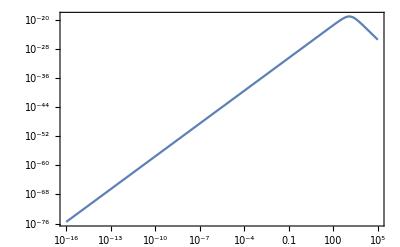

```mathematica
LogLogPlot[Ωsou[f,0.5,αλmin,βHλmin,Tnλmin],{f,10^-16,10^5}]
```

### Turbulence

```mathematica
κtur[vb_,α_]=.05*κ[vb,α];
(*Plasma turbulence*)
ftur[vb_,βH_,Tn_]:=2.7/vb*10^(-5)*βH*(Tn/100)*(100/100)^(1/6);
(*A peak frequency of the turbulence*)
hstar[Tn_]:=16.5*10^(-6)*(Tn/100)*(100/100)^(1/6);
(*Hubble paramter at Subscript[T, n]*)
Ωtur[f_,vb_,α_,βH_,Tn_]:=3.35*10^(-4)/βH*(κtur[vb,α]*α/(1+α))^(3/2)*(100/100)^(1/3)*vb*(f/ftur[vb,βH,Tn])^3/(1+f/(ftur[vb,βH,Tn]))^(11/3)/(1+8π*f/hstar[Tn])
```

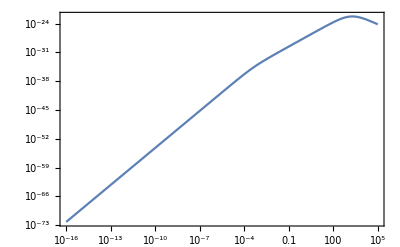

```mathematica
LogLogPlot[Ωtur[f,0.5,αλmin,βHλmin,Tnλmin],{f,10^-16,10^5}]
```

### Sum

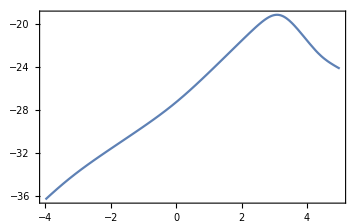

```mathematica
myTicks[lower_,upper_,step_]:=Flatten[Module[{Local=#,LocalTicks},LocalTicks=Log[10,Range[10^(#-1),10^#,(10^#-10^(#-1))/(10-1)]];
Join[{#,""}&/@Most[LocalTicks],{{Last[LocalTicks],Which[Last[LocalTicks]==0,1,Last[LocalTicks]==1,10,True,Power[10,ToString[Last[LocalTicks]]]],{0.03,0}(*longer ticks*)}}]]&/@Range[lower,upper,step],1];
myTicksMajor[lower_,upper_,step_]:=Join[Table[{i,Which[i==0,1,Mod[i,step]==0,Power[10,ToString[i]],True,Null]},{i,lower,upper}]];
slow=Plot[Log10[Ωsou[10^logf,0.5,αλmin,βHλmin,Tnλmin]+Ωtur[10^logf,0.5,αλmin,βHλmin,Tnλmin]],{logf,-4,5},Axes->None]
```

## GW in high wall speed

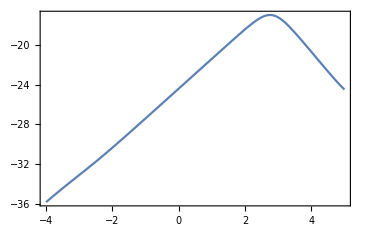

```mathematica
fsou[vb_,βH_,Tn_]:=1.9*10^(-5)*(100/100)^(1/6)*(Tn/100)*(βH)/vb;
κ[α_]:=α/(0.73+0.083Sqrt[α]+α);
Ωsou[f_,vb_,α_,βH_,Tn_]:=2.65*10^(-6)*vb*(100/100)^(1/3)/βH*(κ[α]*α/(1+α))^2*(7^(7/2)*(f/fsou[vb,βH,Tn])^3/(4+3(f/fsou[vb,βH,Tn])^2)^(7/2));
κtur[α_]=.05*κ[α];
(*Plasma turbulence*)
ftur[vb_,βH_,Tn_]=2.7/vb*10^(-5)*βH*(Tn/100)*(100/100)^(1/6);
(*A peak frequency of the turbulence*)
hstar[Tn_]:=16.5*10^(-6)*(Tn/100)*(100/100)^(1/6);
(*Hubble paramter at Subscript[T, n]*)
Ωtur[f_,vb_,α_,βH_,Tn_]:=3.35*10^(-4)/βH*(κtur[α]*α/(1+α))^(3/2)*(100/100)^(1/3)*vb*(f/ftur[vb,βH,Tn])^3/(1+f/(ftur[vb,βH,Tn]))^(11/3)/(1+8*Pi*f/hstar[Tn]);Fast=Plot[Log10[Ωsou[10^logf,1.0,αλmin,βHλmin,Tnλmin]+Ωtur[10^logf,1.0,αλmin,βHλmin,Tnλmin]],{logf,-4,5},Axes->None]
```

## Observation

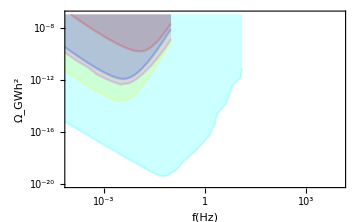

```mathematica
eLISAC4=Import[NotebookDirectory[]<>"LISAC4.csv"];
eLISAC3=Import[NotebookDirectory[]<>"LISAC3.csv"];
eLISAC2=Import[NotebookDirectory[]<>"LISAC2.csv"];
eLISAC1=Import[NotebookDirectory[]<>"LISAC1.csv"];
UD=Import[NotebookDirectory[]<>"UltimateDecigo-Sachiko.csv"];
eLISA=ListLinePlot[{eLISAC4,eLISAC3,eLISAC2,eLISAC1,UD},Filling->Top,ImageSize->Medium,Axes->None,PlotRange->{{-4,4},{-20,-7}},FrameTicks->{{myTicks[-20,-7,2],None},{myTicks[-6,6,1],None}},FrameTicksStyle->{16,Black,FontFamily->"Georgia"},FrameLabel->{Style["f(Hz)",FontFamily->"Georgia",FontSize->16],Style["Ω_GWh^2",FontFamily->"Georgia",FontSize->16]},PlotStyle->{{RGBColor[1,0,0],Opacity[0.2]},{RGBColor[0,0,1],Opacity[0.2]},{RGBColor[1,0,1],Opacity[0.2]},{RGBColor[1,1,0],Opacity[0.2]},{RGBColor[0,1,1],Opacity[0.2]}},Background->White,LabelStyle->{FontFamily->"Georgia",FontSize->16},PlotRangePadding->None]
```

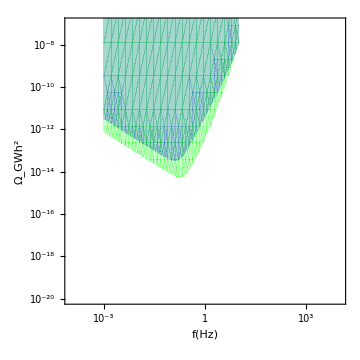

```mathematica
DECIGOandBBO=RegionPlot[{y>Log10[(3*10^17)^2*2*Pi^2/3*(10^f)^3(7.05*10^(-48)*(1+(10^f/7.36)^2)+4.8*10^(-51)/10^(4f)/(1+(10^f/7.36)^2)+5.33*10^(-52)10^(-4f))],y>Log10[(3*10^17)^2*2*Pi^2/3*(10^f)^3(2*10^(-49)*10^(2f)+4.58*10^(-49)+1.26*10^(-51)*10^(-4f))]},{f,-3,1},{y,-30,0},ImageSize->Medium,Axes->None,PlotRange->{{-4,4},{-20,-7}},FrameTicks->{{myTicks[-20,-7,2],None},{myTicks[-6,6,1],None}},FrameTicksStyle->{16,Black,FontFamily->"Georgia"},FrameLabel->{Style["f(Hz)",FontFamily->"Georgia",FontSize->16],Style["Ω_GWh^2",FontFamily->"Georgia",FontSize->16]},Background->White,LabelStyle->{FontFamily->"Georgia",FontSize->16},PlotRangePadding->None,PlotStyle->{{RGBColor[0,0,1],Opacity[0.2]},{RGBColor[0,1,0],Opacity[0.2]}},BoundaryStyle->None]
```

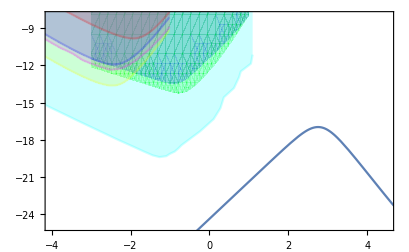

```mathematica
Show[Fast,DECIGOandBBO,eLISA,PlotRange->{{-4,4.5},{-25,-8}}]
```